1 - 6 Bases: typical examples
To get a feel for higher order ODEs, show that the given functions are solutions and form a basis on any interval. Use Wronskians. In problem 6, x > 0,

1.  1, x, x^2, x^3, y^iv=0

```mathematica
Clear["Global`*"]
```

```mathematica
gelb=y''''[x]==0
relb=DSolve[gelb,y[x],x]
```

y^(4)[x]==0

{{y[x]→C[1]+x C[2]+x^2 C[3]+x^3 C[4]}}

1. Above: When the constants for all factors except the factor of interest become zero, the factor of interest is shown to be a sol’n.

2. Above: By inspection, a set of four members. A factor of x is part of any multiplication expression applied to any member with the intention of yielding a transformation between members. Therefore the members are linearly independent. Since all four members are sol’ns, and they are linearly independent, they form a basis.

```mathematica
Clear["Global`*"]
```

```mathematica
Wronskian[{1,x,x^2,x^3},x]
```

12

3. The Wronskian is non-zero, another proof that the four members form a basis.

3.  Cos[x], Sin[x], x Cos[x], x Sin[x],  y^iv+2 y''=0

```mathematica
Clear["Global`*"]
```

```mathematica
eqn1=Solve[Cos[x]==a Sin[x],a]
```

{{a→Cot[x]}}

```mathematica
eqn2=Solve[Cos[x]==a x Cos[x],a]
```

{{a→1/x}}

```mathematica
eqn3=Solve[Cos[x]==a x Sin[x],a]
```

{{a→Cot[x]/x}}

```mathematica
eqn5=Solve[Sin[x]==a x Cos[x],a]
```

{{a→Tan[x]/x}}

```mathematica
eqn6=Solve[Sin[x]==a x Sin[x],a]
```

{{a→1/x}}

```mathematica
eqn7=Solve[x Cos[x]==a x Sin[x],a]
```

{{a→Cot[x]}}

1. Above: The six Solve equations examine relationships among all four of the members of this set. Since none of the links between members represented by a (or 1/a) is a constant value, the four must be linearly independent.

```mathematica
happ=DSolve[y''''[x]+2 y''[x]+y[x]==0,y[x],x]
```

{{y[x]→C[1] Cos[x]+x C[2] Cos[x]+C[3] Sin[x]+x C[4] Sin[x]}}

```mathematica
happ[[1,1,2,1]]
```

C[1] Cos[x]

```mathematica
TableForm[Table[{Subscript[y, n][x],happ[[1,1,2,n]]},{n,4}],TableHeadings->{{},{"y_n[x] " , " set member"}}]
```

| y_n[x]  |  set member
 | y_1[x] | C[1] Cos[x]
 | y_2[x] | x C[2] Cos[x]
 | y_3[x] | C[3] Sin[x]
 | y_4[x] | x C[4] Sin[x]

2. Above: All four of the set members listed in the problem description show up as sol’ns to the DE, and are listed in the table above. Assignment of appropriate constants makes each stand alone sequentially as a sol’n.

```mathematica
Wronskian[{Cos[x],Sin[x],x Cos[x],x Sin[x]},x]
```

4

3. Above: The non-zero value of the Wronskian adds another proof of linear independence.

5.  1, ⅇ^-x Cos[2 x], ⅇ^-x Sin[2x], y'''+2y''+5y'=0

```mathematica
Clear["Global`*"]
```

```mathematica
Wronskian[{1,ⅇ^-x Cos[2 x],ⅇ^-x Sin[2 x]},x]
```

10 ⅇ^(-2 x)

```mathematica
Limit[10 ⅇ^(-2 x),x->∞]
```

0

1. Above: The question is whether these three functions do form a basis “. . . on any interval”. From the text and from a web site, http://tutorial.math.lamar.edu/Classes/DE/Wronskian.aspx, I find that to be linearly dependent, the functions (or at least two anyway) have to be identically zero for all x on the open interval.

```mathematica
excos2x=TableForm[Table[{n D ,D[ⅇ^-x Cos[2 x],{x,n}]},{n,0,4}],TableHeadings->{{},{"order " , "differentiation term"}}]
```

| order  | differentiation term
 | 0 | ⅇ^-x Cos[2 x]
 | D | -ⅇ^-x Cos[2 x]-2 ⅇ^-x Sin[2 x]
 | 2 D | -3 ⅇ^-x Cos[2 x]+4 ⅇ^-x Sin[2 x]
 | 3 D | 11 ⅇ^-x Cos[2 x]+2 ⅇ^-x Sin[2 x]
 | 4 D | -7 ⅇ^-x Cos[2 x]-24 ⅇ^-x Sin[2 x]

```mathematica
arc=Simplify[(11 ⅇ^-x Cos[2 x]+2 ⅇ^-x Sin[2 x])+2 (-3 ⅇ^-x Cos[2 x]+4 ⅇ^-x Sin[2 x])+5 (-ⅇ^-x Cos[2 x]-2 ⅇ^-x Sin[2 x])]
```

0

2. Above: the zero demonstrates that ⅇ^-x Cos[2 x] is a sol’n to the problem equation.

```mathematica
exsin2x=TableForm[Table[{n D ,D[ⅇ^-x Sin[2 x],{x,n}]},{n,0,4}],TableHeadings->{{},{"order " , "differentiation term"}}]
```

| order  | differentiation term
 | 0 | ⅇ^-x Sin[2 x]
 | D | 2 ⅇ^-x Cos[2 x]-ⅇ^-x Sin[2 x]
 | 2 D | -4 ⅇ^-x Cos[2 x]-3 ⅇ^-x Sin[2 x]
 | 3 D | -2 ⅇ^-x Cos[2 x]+11 ⅇ^-x Sin[2 x]
 | 4 D | 24 ⅇ^-x Cos[2 x]-7 ⅇ^-x Sin[2 x]

```mathematica
barc=Simplify[(-2 ⅇ^-x Cos[2 x]+11 ⅇ^-x Sin[2 x])+2 (-4 ⅇ^-x Cos[2 x]-3 ⅇ^-x Sin[2 x])+5 (2 ⅇ^-x Cos[2 x]-ⅇ^-x Sin[2 x])]
```

0

3. Above: the zero demonstrates that ⅇ^-x Sin[2 x] is a sol’n to the problem equation.
4. The number 1 is obviously a sol’n to the problem equation. Thus all set members are sol’ns.

8 - 15 Linear independence
Are the given functions linearly independent or dependent on the half-axis x ≥ 0? Give reason.

9.  Tan[x], Cot[x], 1

```mathematica
Clear["Global`*"]
```

```mathematica
elp=Wronskian[{Tan[x],Cot[x],1},x]
```

16 Csc[2 x]^3

The Wronskian is not identically zero for all x on the half open interval [0,∞); therefore the functions are linearly independent.

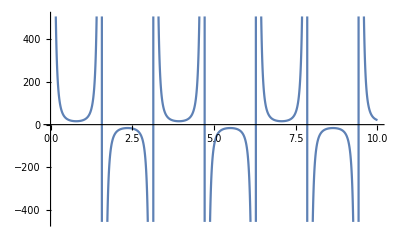

```mathematica
Plot[elp,{x,0,10},PlotRange->Automatic]
```

```mathematica
plot1=Plot[Tan[x],{x,0,10},PlotRange->Automatic];
```

```mathematica
plot2=Plot[Cot[x],{x,0,10},PlotRange->Automatic];
plot3=Plot[1,{x,0,10},PlotRange->Automatic];
```

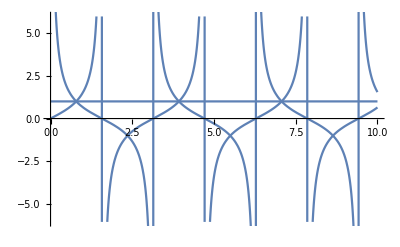

```mathematica
Show[plot1,plot2,plot3]
```

11.  ⅇ^x Cos[x], ⅇ^x Sin[x], ⅇ^x

```mathematica
Clear["Global`*"]
```

```mathematica
Wronskian[{ⅇ^x Cos[x],ⅇ^x Sin[x],ⅇ^x},x]
```

ⅇ^(3 x)

The Wronskian is non-zero on the open interval (-∞,∞); therefore the functions are linearly independent.

13.  Sin[x], Cos[x], Sin[2 x]

```mathematica
Clear["Global`*"]
```

```mathematica
Wronskian[{Sin[x],Cos[x],Sin[2 x]},x]
```

3 Sin[2 x]

Every π/2, the function equals zero, but that should not be a problem for linear independence; the Wronskian is non-zero for all other points, and the functions are linearly independent.

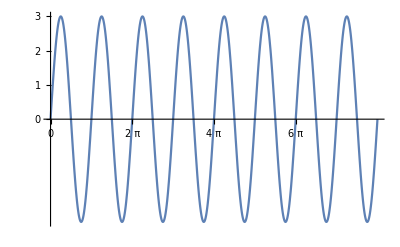

```mathematica
Plot[3 Sin[2 x],{x,0,8 π},PlotRange->Automatic,Ticks->{{0,π, 2π ,3π,4π,5π,6π},{0,1,2,3}}]
```

15.  Cosh[2x], Sinh[2x], ⅇ^(2x)

```mathematica
Clear["Global`*"]
```

```mathematica
Wronskian[{Cosh[2 x],Sinh[2 x],ⅇ^(2 x)},x]
```

0

Finally, dependence! The Wronskian equal to zero means that the functions are linearly dependent on the open interval.